```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
data=Join[Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL000``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"t (s)"->1,"V (V)"->2|>]&/@Range[1,9],Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL00``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"t (s)"->1,"V (V)"->2|>]&/@Range[10,17]];
```

```mathematica
Length@data
```

17

```mathematica
data3to7=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{3,7}];
```

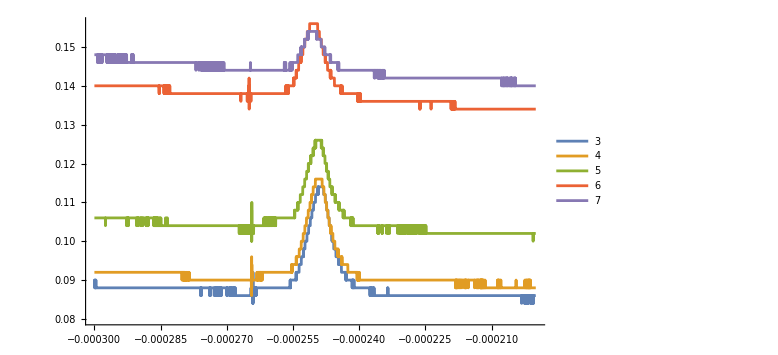

```mathematica
ListLinePlot[data3to7,ImageSize->Large,PlotLegends->Placed[Range[3,7],Below]]
```

```mathematica
data8to12=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{8,12}];
```

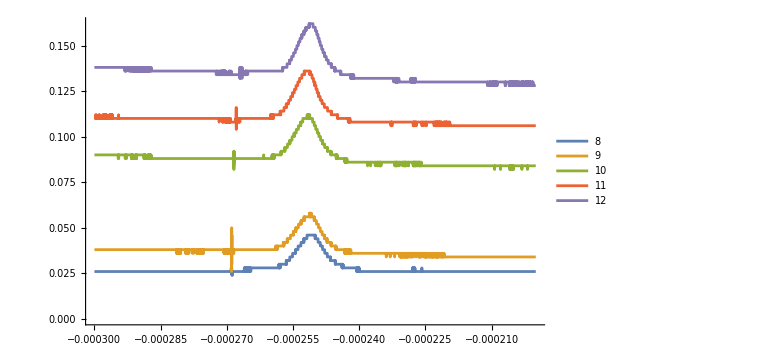

```mathematica
ListLinePlot[data8to12,ImageSize->Large,PlotLegends->Placed[Range[8,12],Below]]
```

```mathematica
data13to17=Transpose[{#[All,"t (s)"],#[All,"V (V)"]}//Normal]&/@Take[data,{13,17}];
```

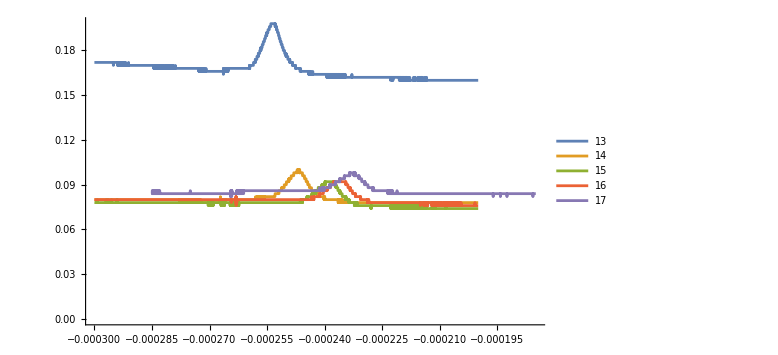

```mathematica
ListLinePlot[data13to17,ImageSize->Large,PlotLegends->Placed[Range[13,17],Below]]
```

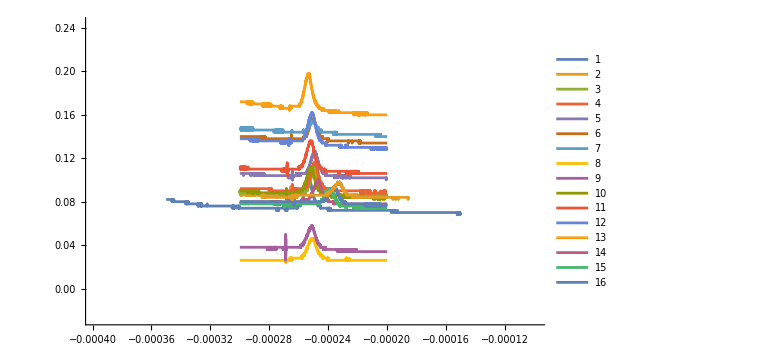

```mathematica
ListLinePlot[data2,PlotLegends->Placed[Range[1,17],Below],ImageSize->Large]
```

```mathematica
datalast=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/HS/data/ALL00``.CSV",#],"Table","HeaderLines"->18,"FieldSeparators"->",","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,4]][All,<|"t_1 (s)"->1,"V_x (V)"->2,"t_2 (s)"->3,"V_y (V)"->4|>]&/@Range[18,19];
```

```mathematica
datalast2=Transpose[{#[All,"V_x (V)"],#[All,"V_y (V)"]}//Normal]&/@datalast;
```

```mathematica
Length@First@datalast2
```

5000

```mathematica
fit=NonlinearModelFit[First@datalast2,-a Exp[k (x-x0)]+b,{a,b,k,x0},x]
```

FittedModel[1.24089-0.00704839 ⅇ^(0.695075 (-1.53499+x))]

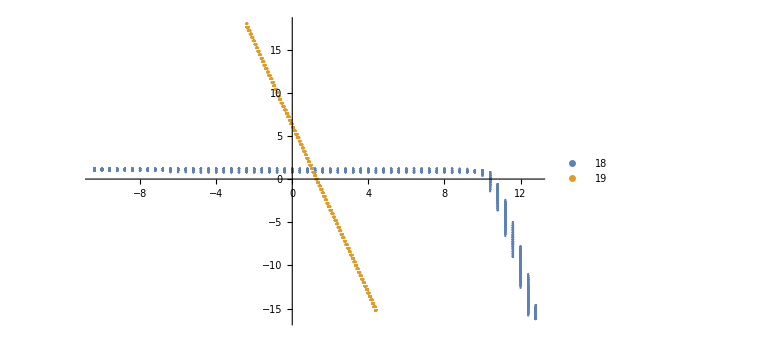

```mathematica
Show[ListPlot[datalast2,ImageSize->Large,PlotLegends->Placed[{18,19},Below],PlotRange->All](*,Plot[fit[x],{x,-10,18},ImageSize->Large,PlotStyle->{Dashed,Orange}]*)]
```